# EDUS_2.0 HDF5 parser

## Initialization, first imports

### kernel definitions

```mathematica
LaunchKernels[16]
```

{Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16)}

```mathematica
ParallelEvaluate[
$HistoryLength=0;
SetSystemOptions["CacheOptions"->{"Numeric"->{"Cache"->False},"Symbolic"->{"Cache"->False}}];
]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Needs["GeneralUtilities`"]
```

```mathematica
ClearSystemCache[]
$HistoryLength=0;
SetSystemOptions["CacheOptions"->{"Numeric"->{"Cache"->False},"Symbolic"->{"Cache"->False}}];
```

```mathematica
<<MaTeX`
texStyle={FontFamily->"CMU Serif",FontColor->Black,FontSize->22};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb}","\\usepackage{xcolor,color}"}];
MaTLabel[text_,size_]:=Style[MaTeX[text,FontSize->size]];
SetDirectory[NotebookDirectory[]]

$Assumptions=k∈PositiveReals;
```

/home/mauricioquintela/Dropbox/UAM-postdoc/edus_post-process

### initial h5 read

```mathematica
tt="./output.h5";
```

```mathematica
h5=Import[tt];
```

```mathematica
Import[tt,"/json/laser0/"]
```

<|cycles→{1},frequency→{5.},intensity→{1.×10^6},polarization→{1},wavelength→{1.02514×10^10}|>

```mathematica
h5clean=Last/@Sort[{ToExpression[StringJoin[Select[Characters@#,DigitQ]]],#}&/@h5]
```

{/DensityMatrix_k/0/0/local,/DensityMatrix_k_bloch/0/0/local,/fullH/0/0/local,/json/laser0/cycles,/json/laser0/frequency,/json/laser0/intensity,/json/laser0/polarization,/json/laser0/wavelength,/SelfEnergy/0/0/local,/DensityMatrix_k/1/0/local,/DensityMatrix_k_bloch/1/0/local,/fullH/1/0/local,/SelfEnergy/1/0/local,/DensityMatrix_k/2/0/local,/DensityMatrix_k_bloch/2/0/local,/fullH/2/0/local,/SelfEnergy/2/0/local,/DensityMatrix_k/3/0/local,/DensityMatrix_k_bloch/3/0/local,/fullH/3/0/local,/SelfEnergy/3/0/local,/DensityMatrix_k/4/0/local,/DensityMatrix_k_bloch/4/0/local,/fullH/4/0/local,/SelfEnergy/4/0/local,/DensityMatrix_k/5/0/local,/DensityMatrix_k_bloch/5/0/local,/fullH/5/0/local,/SelfEnergy/5/0/local,/DensityMatrix_k/6/0/local,/DensityMatrix_k_bloch/6/0/local,/fullH/6/0/local,/SelfEnergy/6/0/local,/DensityMatrix_k/7/0/local,/DensityMatrix_k_bloch/7/0/local,/fullH/7/0/local,/SelfEnergy/7/0/local,/DensityMatrix_k/8/0/local,/DensityMatrix_k_bloch/8/0/local,/fullH/8/0/local,/SelfEnergy/8/0/local,/DensityMatrix_k/9/0/local,/DensityMatrix_k_bloch/9/0/local,/fullH/9/0/local,/SelfEnergy/9/0/local,/DensityMatrix_k/10/0/local,/DensityMatrix_k_bloch/10/0/local,/fullH/10/0/local,/SelfEnergy/10/0/local,/DensityMatrix_k/11/0/local,/DensityMatrix_k_bloch/11/0/local,/fullH/11/0/local,/SelfEnergy/11/0/local,/DensityMatrix_k/12/0/local,/DensityMatrix_k_bloch/12/0/local,/fullH/12/0/local,/SelfEnergy/12/0/local,/DensityMatrix_k/13/0/local,/DensityMatrix_k_bloch/13/0/local,/fullH/13/0/local,/SelfEnergy/13/0/local,/DensityMatrix_k/14/0/local,/DensityMatrix_k_bloch/14/0/local,/fullH/14/0/local,/SelfEnergy/14/0/local,/DensityMatrix_k/15/0/local,/DensityMatrix_k_bloch/15/0/local,/fullH/15/0/local,/SelfEnergy/15/0/local,/DensityMatrix_k/16/0/local,/DensityMatrix_k_bloch/16/0/local,/fullH/16/0/local,/SelfEnergy/16/0/local,/DensityMatrix_k/17/0/local,/DensityMatrix_k_bloch/17/0/local,/fullH/17/0/local,/SelfEnergy/17/0/local,/DensityMatrix_k/18/0/local,/DensityMatrix_k_bloch/18/0/local,/fullH/18/0/local,/SelfEnergy/18/0/local,/DensityMatrix_k/19/0/local,/DensityMatrix_k_bloch/19/0/local,/fullH/19/0/local,/SelfEnergy/19/0/local,/DensityMatrix_k/20/0/local,/DensityMatrix_k_bloch/20/0/local,/fullH/20/0/local,/SelfEnergy/20/0/local,/DensityMatrix_k/21/0/local,/DensityMatrix_k_bloch/21/0/local,/fullH/21/0/local,/SelfEnergy/21/0/local,/DensityMatrix_k/22/0/local,/DensityMatrix_k_bloch/22/0/local,/fullH/22/0/local,/SelfEnergy/22/0/local,/DensityMatrix_k/23/0/local,/DensityMatrix_k_bloch/23/0/local,/fullH/23/0/local,/SelfEnergy/23/0/local,/DensityMatrix_k/24/0/local,/DensityMatrix_k_bloch/24/0/local,/fullH/24/0/local,/SelfEnergy/24/0/local,/DensityMatrix_k/25/0/local,/DensityMatrix_k_bloch/25/0/local,/fullH/25/0/local,/SelfEnergy/25/0/local,/DensityMatrix_k/26/0/local,/DensityMatrix_k_bloch/26/0/local,/fullH/26/0/local,/SelfEnergy/26/0/local,/DensityMatrix_k/27/0/local,/DensityMatrix_k_bloch/27/0/local,/fullH/27/0/local,/SelfEnergy/27/0/local,/DensityMatrix_k/28/0/local,/DensityMatrix_k_bloch/28/0/local,/fullH/28/0/local,/SelfEnergy/28/0/local,/DensityMatrix_k/29/0/local,/DensityMatrix_k_bloch/29/0/local,/fullH/29/0/local,/SelfEnergy/29/0/local,/DensityMatrix_k/30/0/local,/DensityMatrix_k_bloch/30/0/local,/fullH/30/0/local,/SelfEnergy/30/0/local,/DensityMatrix_k/31/0/local,/DensityMatrix_k_bloch/31/0/local,/fullH/31/0/local,/SelfEnergy/31/0/local,/DensityMatrix_k/32/0/local,/DensityMatrix_k_bloch/32/0/local,/fullH/32/0/local,/SelfEnergy/32/0/local,/DensityMatrix_k/33/0/local,/DensityMatrix_k_bloch/33/0/local,/fullH/33/0/local,/SelfEnergy/33/0/local,/DensityMatrix_k/34/0/local,/DensityMatrix_k_bloch/34/0/local,/fullH/34/0/local,/SelfEnergy/34/0/local,/DensityMatrix_k/35/0/local,/DensityMatrix_k_bloch/35/0/local,/fullH/35/0/local,/SelfEnergy/35/0/local,/DensityMatrix_k/36/0/local,/DensityMatrix_k_bloch/36/0/local,/fullH/36/0/local,/SelfEnergy/36/0/local,/DensityMatrix_k/37/0/local,/DensityMatrix_k_bloch/37/0/local,/fullH/37/0/local,/SelfEnergy/37/0/local,/DensityMatrix_k/38/0/local,/DensityMatrix_k_bloch/38/0/local,/fullH/38/0/local,/SelfEnergy/38/0/local,/DensityMatrix_k/39/0/local,/DensityMatrix_k_bloch/39/0/local,/fullH/39/0/local,/SelfEnergy/39/0/local,/DensityMatrix_k/40/0/local,/DensityMatrix_k_bloch/40/0/local,/fullH/40/0/local,/SelfEnergy/40/0/local,/DensityMatrix_k/41/0/local,/DensityMatrix_k_bloch/41/0/local,/fullH/41/0/local,/SelfEnergy/41/0/local,/DensityMatrix_k/42/0/local,/DensityMatrix_k_bloch/42/0/local,/fullH/42/0/local,/SelfEnergy/42/0/local,/DensityMatrix_k/43/0/local,/DensityMatrix_k_bloch/43/0/local,/fullH/43/0/local,/SelfEnergy/43/0/local,/DensityMatrix_k/44/0/local,/DensityMatrix_k_bloch/44/0/local,/fullH/44/0/local,/SelfEnergy/44/0/local,/DensityMatrix_k/45/0/local,/DensityMatrix_k_bloch/45/0/local,/fullH/45/0/local,/SelfEnergy/45/0/local,/DensityMatrix_k/46/0/local,/DensityMatrix_k_bloch/46/0/local,/fullH/46/0/local,/SelfEnergy/46/0/local,/DensityMatrix_k/47/0/local,/DensityMatrix_k_bloch/47/0/local,/fullH/47/0/local,/SelfEnergy/47/0/local,/DensityMatrix_k/48/0/local,/DensityMatrix_k_bloch/48/0/local,/fullH/48/0/local,/SelfEnergy/48/0/local,/DensityMatrix_k/49/0/local,/DensityMatrix_k_bloch/49/0/local,/fullH/49/0/local,/SelfEnergy/49/0/local,/DensityMatrix_k/50/0/local,/DensityMatrix_k_bloch/50/0/local,/fullH/50/0/local,/SelfEnergy/50/0/local,/DensityMatrix_k/51/0/local,/DensityMatrix_k_bloch/51/0/local,/fullH/51/0/local,/SelfEnergy/51/0/local,/DensityMatrix_k/52/0/local,/DensityMatrix_k_bloch/52/0/local,/fullH/52/0/local,/SelfEnergy/52/0/local,/DensityMatrix_k/53/0/local,/DensityMatrix_k_bloch/53/0/local,/fullH/53/0/local,/SelfEnergy/53/0/local,/DensityMatrix_k/54/0/local,/DensityMatrix_k_bloch/54/0/local,/fullH/54/0/local,/SelfEnergy/54/0/local,/DensityMatrix_k/55/0/local,/DensityMatrix_k_bloch/55/0/local,/fullH/55/0/local,/SelfEnergy/55/0/local,/DensityMatrix_k/56/0/local,/DensityMatrix_k_bloch/56/0/local,/fullH/56/0/local,/SelfEnergy/56/0/local,/DensityMatrix_k/57/0/local,/DensityMatrix_k_bloch/57/0/local,/fullH/57/0/local,/SelfEnergy/57/0/local,/DensityMatrix_k/58/0/local,/DensityMatrix_k_bloch/58/0/local,/fullH/58/0/local,/SelfEnergy/58/0/local,/DensityMatrix_k/59/0/local,/DensityMatrix_k_bloch/59/0/local,/fullH/59/0/local,/SelfEnergy/59/0/local,/DensityMatrix_k/60/0/local,/DensityMatrix_k_bloch/60/0/local,/fullH/60/0/local,/SelfEnergy/60/0/local,/DensityMatrix_k/61/0/local,/DensityMatrix_k_bloch/61/0/local,/fullH/61/0/local,/SelfEnergy/61/0/local,/DensityMatrix_k/62/0/local,/DensityMatrix_k_bloch/62/0/local,/fullH/62/0/local,/SelfEnergy/62/0/local,/DensityMatrix_k/63/0/local,/DensityMatrix_k_bloch/63/0/local,/fullH/63/0/local,/SelfEnergy/63/0/local,/DensityMatrix_k/64/0/local,/DensityMatrix_k_bloch/64/0/local,/fullH/64/0/local,/SelfEnergy/64/0/local,/DensityMatrix_k/65/0/local,/DensityMatrix_k_bloch/65/0/local,/fullH/65/0/local,/SelfEnergy/65/0/local,/DensityMatrix_k/66/0/local,/DensityMatrix_k_bloch/66/0/local,/fullH/66/0/local,/SelfEnergy/66/0/local,/DensityMatrix_k/67/0/local,/DensityMatrix_k_bloch/67/0/local,/fullH/67/0/local,/SelfEnergy/67/0/local,/DensityMatrix_k/68/0/local,/DensityMatrix_k_bloch/68/0/local,/fullH/68/0/local,/SelfEnergy/68/0/local,/DensityMatrix_k/69/0/local,/DensityMatrix_k_bloch/69/0/local,/fullH/69/0/local,/SelfEnergy/69/0/local,/DensityMatrix_k/70/0/local,/DensityMatrix_k_bloch/70/0/local,/fullH/70/0/local,/SelfEnergy/70/0/local,/DensityMatrix_k/71/0/local,/DensityMatrix_k_bloch/71/0/local,/fullH/71/0/local,/SelfEnergy/71/0/local,/DensityMatrix_k/72/0/local,/DensityMatrix_k_bloch/72/0/local,/fullH/72/0/local,/SelfEnergy/72/0/local,/DensityMatrix_k/73/0/local,/DensityMatrix_k_bloch/73/0/local,/fullH/73/0/local,/SelfEnergy/73/0/local,/DensityMatrix_k/74/0/local,/DensityMatrix_k_bloch/74/0/local,/fullH/74/0/local,/SelfEnergy/74/0/local,/DensityMatrix_k/75/0/local,/DensityMatrix_k_bloch/75/0/local,/fullH/75/0/local,/SelfEnergy/75/0/local,/DensityMatrix_k/76/0/local,/DensityMatrix_k_bloch/76/0/local,/fullH/76/0/local,/SelfEnergy/76/0/local,/DensityMatrix_k/77/0/local,/DensityMatrix_k_bloch/77/0/local,/fullH/77/0/local,/SelfEnergy/77/0/local,/DensityMatrix_k/78/0/local,/DensityMatrix_k_bloch/78/0/local,/fullH/78/0/local,/SelfEnergy/78/0/local,/DensityMatrix_k/79/0/local,/DensityMatrix_k_bloch/79/0/local,/fullH/79/0/local,/SelfEnergy/79/0/local,/DensityMatrix_k/80/0/local,/DensityMatrix_k_bloch/80/0/local,/fullH/80/0/local,/SelfEnergy/80/0/local,/DensityMatrix_k/81/0/local,/DensityMatrix_k_bloch/81/0/local,/fullH/81/0/local,/SelfEnergy/81/0/local,/DensityMatrix_k/82/0/local,/DensityMatrix_k_bloch/82/0/local,/fullH/82/0/local,/SelfEnergy/82/0/local,/DensityMatrix_k/83/0/local,/DensityMatrix_k_bloch/83/0/local,/fullH/83/0/local,/SelfEnergy/83/0/local,/DensityMatrix_k/84/0/local,/DensityMatrix_k_bloch/84/0/local,/fullH/84/0/local,/SelfEnergy/84/0/local,/DensityMatrix_k/85/0/local,/DensityMatrix_k_bloch/85/0/local,/fullH/85/0/local,/SelfEnergy/85/0/local,/DensityMatrix_k/86/0/local,/DensityMatrix_k_bloch/86/0/local,/fullH/86/0/local,/SelfEnergy/86/0/local,/DensityMatrix_k/87/0/local,/DensityMatrix_k_bloch/87/0/local,/fullH/87/0/local,/SelfEnergy/87/0/local,/DensityMatrix_k/88/0/local,/DensityMatrix_k_bloch/88/0/local,/fullH/88/0/local,/SelfEnergy/88/0/local,/DensityMatrix_k/89/0/local,/DensityMatrix_k_bloch/89/0/local,/fullH/89/0/local,/SelfEnergy/89/0/local,/DensityMatrix_k/90/0/local,/DensityMatrix_k_bloch/90/0/local,/fullH/90/0/local,/SelfEnergy/90/0/local,/DensityMatrix_k/91/0/local,/DensityMatrix_k_bloch/91/0/local,/fullH/91/0/local,/SelfEnergy/91/0/local,/DensityMatrix_k/92/0/local,/DensityMatrix_k_bloch/92/0/local,/fullH/92/0/local,/SelfEnergy/92/0/local,/DensityMatrix_k/93/0/local,/DensityMatrix_k_bloch/93/0/local,/fullH/93/0/local,/SelfEnergy/93/0/local,/DensityMatrix_k/94/0/local,/DensityMatrix_k_bloch/94/0/local,/fullH/94/0/local,/SelfEnergy/94/0/local,/DensityMatrix_k/95/0/local,/DensityMatrix_k_bloch/95/0/local,/fullH/95/0/local,/SelfEnergy/95/0/local,/DensityMatrix_k/96/0/local,/DensityMatrix_k_bloch/96/0/local,/fullH/96/0/local,/SelfEnergy/96/0/local,/DensityMatrix_k/97/0/local,/DensityMatrix_k_bloch/97/0/local,/fullH/97/0/local,/SelfEnergy/97/0/local,/DensityMatrix_k/98/0/local,/DensityMatrix_k_bloch/98/0/local,/fullH/98/0/local,/SelfEnergy/98/0/local,/DensityMatrix_k/99/0/local,/DensityMatrix_k_bloch/99/0/local,/fullH/99/0/local,/SelfEnergy/99/0/local,/DensityMatrix_k/100/0/local,/DensityMatrix_k_bloch/100/0/local,/fullH/100/0/local,/SelfEnergy/100/0/local,/DensityMatrix_k/101/0/local,/DensityMatrix_k_bloch/101/0/local,/fullH/101/0/local,/SelfEnergy/101/0/local,/DensityMatrix_k/102/0/local,/DensityMatrix_k_bloch/102/0/local,/fullH/102/0/local,/SelfEnergy/102/0/local,/DensityMatrix_k/103/0/local,/DensityMatrix_k_bloch/103/0/local,/fullH/103/0/local,/SelfEnergy/103/0/local,/DensityMatrix_k/104/0/local,/DensityMatrix_k_bloch/104/0/local,/fullH/104/0/local,/SelfEnergy/104/0/local,/DensityMatrix_k/105/0/local,/DensityMatrix_k_bloch/105/0/local,/fullH/105/0/local,/SelfEnergy/105/0/local,/DensityMatrix_k/106/0/local,/DensityMatrix_k_bloch/106/0/local,/fullH/106/0/local,/SelfEnergy/106/0/local,/DensityMatrix_k/107/0/local,/DensityMatrix_k_bloch/107/0/local,/fullH/107/0/local,/SelfEnergy/107/0/local,/DensityMatrix_k/108/0/local,/DensityMatrix_k_bloch/108/0/local,/fullH/108/0/local,/SelfEnergy/108/0/local,/DensityMatrix_k/109/0/local,/DensityMatrix_k_bloch/109/0/local,/fullH/109/0/local,/SelfEnergy/109/0/local,/DensityMatrix_k/110/0/local,/DensityMatrix_k_bloch/110/0/local,/fullH/110/0/local,/SelfEnergy/110/0/local,/DensityMatrix_k/111/0/local,/DensityMatrix_k_bloch/111/0/local,/fullH/111/0/local,/SelfEnergy/111/0/local,/DensityMatrix_k/112/0/local,/DensityMatrix_k_bloch/112/0/local,/fullH/112/0/local,/SelfEnergy/112/0/local,/DensityMatrix_k/113/0/local,/DensityMatrix_k_bloch/113/0/local,/fullH/113/0/local,/SelfEnergy/113/0/local,/DensityMatrix_k/114/0/local,/DensityMatrix_k_bloch/114/0/local,/fullH/114/0/local,/SelfEnergy/114/0/local,/DensityMatrix_k/115/0/local,/DensityMatrix_k_bloch/115/0/local,/fullH/115/0/local,/SelfEnergy/115/0/local,/DensityMatrix_k/116/0/local,/DensityMatrix_k_bloch/116/0/local,/fullH/116/0/local,/SelfEnergy/116/0/local,/DensityMatrix_k/117/0/local,/DensityMatrix_k_bloch/117/0/local,/fullH/117/0/local,/SelfEnergy/117/0/local,/DensityMatrix_k/118/0/local,/DensityMatrix_k_bloch/118/0/local,/fullH/118/0/local,/SelfEnergy/118/0/local,/DensityMatrix_k/119/0/local,/DensityMatrix_k_bloch/119/0/local,/fullH/119/0/local,/SelfEnergy/119/0/local,/DensityMatrix_k/120/0/local,/DensityMatrix_k_bloch/120/0/local,/fullH/120/0/local,/SelfEnergy/120/0/local,/DensityMatrix_k/121/0/local,/DensityMatrix_k_bloch/121/0/local,/fullH/121/0/local,/SelfEnergy/121/0/local,/DensityMatrix_k/122/0/local,/DensityMatrix_k_bloch/122/0/local,/fullH/122/0/local,/SelfEnergy/122/0/local,/DensityMatrix_k/123/0/local,/DensityMatrix_k_bloch/123/0/local,/fullH/123/0/local,/SelfEnergy/123/0/local,/DensityMatrix_k/124/0/local,/DensityMatrix_k_bloch/124/0/local,/fullH/124/0/local,/SelfEnergy/124/0/local,/DensityMatrix_k/125/0/local,/DensityMatrix_k_bloch/125/0/local,/fullH/125/0/local,/SelfEnergy/125/0/local,/DensityMatrix_k/126/0/local,/DensityMatrix_k_bloch/126/0/local,/fullH/126/0/local,/SelfEnergy/126/0/local,/DensityMatrix_k/127/0/local,/DensityMatrix_k_bloch/127/0/local,/fullH/127/0/local,/SelfEnergy/127/0/local,/DensityMatrix_k/128/0/local,/DensityMatrix_k_bloch/128/0/local,/fullH/128/0/local,/SelfEnergy/128/0/local,/DensityMatrix_k/129/0/local,/DensityMatrix_k_bloch/129/0/local,/fullH/129/0/local,/SelfEnergy/129/0/local,/DensityMatrix_k/130/0/local,/DensityMatrix_k_bloch/130/0/local,/fullH/130/0/local,/SelfEnergy/130/0/local,/DensityMatrix_k/131/0/local,/DensityMatrix_k_bloch/131/0/local,/fullH/131/0/local,/SelfEnergy/131/0/local,/DensityMatrix_k/132/0/local,/DensityMatrix_k_bloch/132/0/local,/fullH/132/0/local,/SelfEnergy/132/0/local,/DensityMatrix_k/133/0/local,/DensityMatrix_k_bloch/133/0/local,/fullH/133/0/local,/SelfEnergy/133/0/local,/DensityMatrix_k/134/0/local,/DensityMatrix_k_bloch/134/0/local,/fullH/134/0/local,/SelfEnergy/134/0/local,/DensityMatrix_k/135/0/local,/DensityMatrix_k_bloch/135/0/local,/fullH/135/0/local,/SelfEnergy/135/0/local,/DensityMatrix_k/136/0/local,/DensityMatrix_k_bloch/136/0/local,/fullH/136/0/local,/SelfEnergy/136/0/local,/DensityMatrix_k/137/0/local,/DensityMatrix_k_bloch/137/0/local,/fullH/137/0/local,/SelfEnergy/137/0/local,/DensityMatrix_k/138/0/local,/DensityMatrix_k_bloch/138/0/local,/fullH/138/0/local,/SelfEnergy/138/0/local,/DensityMatrix_k/139/0/local,/DensityMatrix_k_bloch/139/0/local,/fullH/139/0/local,/SelfEnergy/139/0/local,/DensityMatrix_k/140/0/local,/DensityMatrix_k_bloch/140/0/local,/fullH/140/0/local,/SelfEnergy/140/0/local,/DensityMatrix_k/141/0/local,/DensityMatrix_k_bloch/141/0/local,/fullH/141/0/local,/SelfEnergy/141/0/local,/DensityMatrix_k/142/0/local,/DensityMatrix_k_bloch/142/0/local,/fullH/142/0/local,/SelfEnergy/142/0/local,/DensityMatrix_k/143/0/local,/DensityMatrix_k_bloch/143/0/local,/fullH/143/0/local,/SelfEnergy/143/0/local,/DensityMatrix_k/144/0/local,/DensityMatrix_k_bloch/144/0/local,/fullH/144/0/local,/SelfEnergy/144/0/local,/DensityMatrix_k/145/0/local,/DensityMatrix_k_bloch/145/0/local,/fullH/145/0/local,/SelfEnergy/145/0/local,/DensityMatrix_k/146/0/local,/DensityMatrix_k_bloch/146/0/local,/fullH/146/0/local,/SelfEnergy/146/0/local,/DensityMatrix_k/147/0/local,/DensityMatrix_k_bloch/147/0/local,/fullH/147/0/local,/SelfEnergy/147/0/local,/DensityMatrix_k/148/0/local,/DensityMatrix_k_bloch/148/0/local,/fullH/148/0/local,/SelfEnergy/148/0/local,/DensityMatrix_k/149/0/local,/DensityMatrix_k_bloch/149/0/local,/fullH/149/0/local,/SelfEnergy/149/0/local,/DensityMatrix_k/150/0/local,/DensityMatrix_k_bloch/150/0/local,/fullH/150/0/local,/SelfEnergy/150/0/local,/DensityMatrix_k/151/0/local,/DensityMatrix_k_bloch/151/0/local,/fullH/151/0/local,/SelfEnergy/151/0/local,/DensityMatrix_k/152/0/local,/DensityMatrix_k_bloch/152/0/local,/fullH/152/0/local,/SelfEnergy/152/0/local,/DensityMatrix_k/153/0/local,/DensityMatrix_k_bloch/153/0/local,/fullH/153/0/local,/SelfEnergy/153/0/local,/DensityMatrix_k/154/0/local,/DensityMatrix_k_bloch/154/0/local,/fullH/154/0/local,/SelfEnergy/154/0/local,/DensityMatrix_k/155/0/local,/DensityMatrix_k_bloch/155/0/local,/fullH/155/0/local,/SelfEnergy/155/0/local,/DensityMatrix_k/156/0/local,/DensityMatrix_k_bloch/156/0/local,/fullH/156/0/local,/SelfEnergy/156/0/local,/DensityMatrix_k/157/0/local,/DensityMatrix_k_bloch/157/0/local,/fullH/157/0/local,/SelfEnergy/157/0/local,/DensityMatrix_k/158/0/local,/DensityMatrix_k_bloch/158/0/local,/fullH/158/0/local,/SelfEnergy/158/0/local,/DensityMatrix_k/159/0/local,/DensityMatrix_k_bloch/159/0/local,/fullH/159/0/local,/SelfEnergy/159/0/local,/DensityMatrix_k/160/0/local,/DensityMatrix_k_bloch/160/0/local,/fullH/160/0/local,/SelfEnergy/160/0/local,/DensityMatrix_k/161/0/local,/DensityMatrix_k_bloch/161/0/local,/fullH/161/0/local,/SelfEnergy/161/0/local,/DensityMatrix_k/162/0/local,/DensityMatrix_k_bloch/162/0/local,/fullH/162/0/local,/SelfEnergy/162/0/local,/DensityMatrix_k/163/0/local,/DensityMatrix_k_bloch/163/0/local,/fullH/163/0/local,/SelfEnergy/163/0/local,/DensityMatrix_k/164/0/local,/DensityMatrix_k_bloch/164/0/local,/fullH/164/0/local,/SelfEnergy/164/0/local,/DensityMatrix_k/165/0/local,/DensityMatrix_k_bloch/165/0/local,/fullH/165/0/local,/SelfEnergy/165/0/local,/DensityMatrix_k/166/0/local,/DensityMatrix_k_bloch/166/0/local,/fullH/166/0/local,/SelfEnergy/166/0/local,/DensityMatrix_k/167/0/local,/DensityMatrix_k_bloch/167/0/local,/fullH/167/0/local,/SelfEnergy/167/0/local,/DensityMatrix_k/168/0/local,/DensityMatrix_k_bloch/168/0/local,/fullH/168/0/local,/SelfEnergy/168/0/local,/DensityMatrix_k/169/0/local,/DensityMatrix_k_bloch/169/0/local,/fullH/169/0/local,/SelfEnergy/169/0/local,/DensityMatrix_k/170/0/local,/DensityMatrix_k_bloch/170/0/local,/fullH/170/0/local,/SelfEnergy/170/0/local,/DensityMatrix_k/171/0/local,/DensityMatrix_k_bloch/171/0/local,/fullH/171/0/local,/SelfEnergy/171/0/local,/DensityMatrix_k/172/0/local,/DensityMatrix_k_bloch/172/0/local,/fullH/172/0/local,/SelfEnergy/172/0/local,/DensityMatrix_k/173/0/local,/DensityMatrix_k_bloch/173/0/local,/fullH/173/0/local,/SelfEnergy/173/0/local,/DensityMatrix_k/174/0/local,/DensityMatrix_k_bloch/174/0/local,/fullH/174/0/local,/SelfEnergy/174/0/local,/DensityMatrix_k/175/0/local,/DensityMatrix_k_bloch/175/0/local,/fullH/175/0/local,/SelfEnergy/175/0/local,/DensityMatrix_k/176/0/local,/DensityMatrix_k_bloch/176/0/local,/fullH/176/0/local,/SelfEnergy/176/0/local,/DensityMatrix_k/177/0/local,/DensityMatrix_k_bloch/177/0/local,/fullH/177/0/local,/SelfEnergy/177/0/local,/DensityMatrix_k/178/0/local,/DensityMatrix_k_bloch/178/0/local,/fullH/178/0/local,/SelfEnergy/178/0/local,/DensityMatrix_k/179/0/local,/DensityMatrix_k_bloch/179/0/local,/fullH/179/0/local,/SelfEnergy/179/0/local,/DensityMatrix_k/180/0/local,/DensityMatrix_k_bloch/180/0/local,/fullH/180/0/local,/SelfEnergy/180/0/local,/DensityMatrix_k/181/0/local,/DensityMatrix_k_bloch/181/0/local,/fullH/181/0/local,/SelfEnergy/181/0/local,/DensityMatrix_k/182/0/local,/DensityMatrix_k_bloch/182/0/local,/fullH/182/0/local,/SelfEnergy/182/0/local,/DensityMatrix_k/183/0/local,/DensityMatrix_k_bloch/183/0/local,/fullH/183/0/local,/SelfEnergy/183/0/local,/DensityMatrix_k/184/0/local,/DensityMatrix_k_bloch/184/0/local,/fullH/184/0/local,/SelfEnergy/184/0/local,/DensityMatrix_k/185/0/local,/DensityMatrix_k_bloch/185/0/local,/fullH/185/0/local,/SelfEnergy/185/0/local,/DensityMatrix_k/186/0/local,/DensityMatrix_k_bloch/186/0/local,/fullH/186/0/local,/SelfEnergy/186/0/local,/DensityMatrix_k/187/0/local,/DensityMatrix_k_bloch/187/0/local,/fullH/187/0/local,/SelfEnergy/187/0/local,/DensityMatrix_k/188/0/local,/DensityMatrix_k_bloch/188/0/local,/fullH/188/0/local,/SelfEnergy/188/0/local,/DensityMatrix_k/189/0/local,/DensityMatrix_k_bloch/189/0/local,/fullH/189/0/local,/SelfEnergy/189/0/local,/DensityMatrix_k/190/0/local,/DensityMatrix_k_bloch/190/0/local,/fullH/190/0/local,/SelfEnergy/190/0/local,/DensityMatrix_k/191/0/local,/DensityMatrix_k_bloch/191/0/local,/fullH/191/0/local,/SelfEnergy/191/0/local,/DensityMatrix_k/192/0/local,/DensityMatrix_k_bloch/192/0/local,/fullH/192/0/local,/SelfEnergy/192/0/local,/DensityMatrix_k/193/0/local,/DensityMatrix_k_bloch/193/0/local,/fullH/193/0/local,/SelfEnergy/193/0/local,/DensityMatrix_k/194/0/local,/DensityMatrix_k_bloch/194/0/local,/fullH/194/0/local,/SelfEnergy/194/0/local,/DensityMatrix_k/195/0/local,/DensityMatrix_k_bloch/195/0/local,/fullH/195/0/local,/SelfEnergy/195/0/local,/DensityMatrix_k/196/0/local,/DensityMatrix_k_bloch/196/0/local,/fullH/196/0/local,/SelfEnergy/196/0/local,/DensityMatrix_k/197/0/local,/DensityMatrix_k_bloch/197/0/local,/fullH/197/0/local,/SelfEnergy/197/0/local,/DensityMatrix_k/198/0/local,/DensityMatrix_k_bloch/198/0/local,/fullH/198/0/local,/SelfEnergy/198/0/local,/DensityMatrix_k/199/0/local,/DensityMatrix_k_bloch/199/0/local,/fullH/199/0/local,/SelfEnergy/199/0/local,/DensityMatrix_k/200/0/local,/DensityMatrix_k_bloch/200/0/local,/fullH/200/0/local,/SelfEnergy/200/0/local,/json/A,/json/B,/json/comm_size,/json/coulomb,/json/dt,/json/filledbands,/json/finaltime,/json/grid,/json/initialtime,/json/kpoints,/json/num_bands,/json/num_kpoints,/json/printresolution,/json/solver,/json/tb_file}

### define lattice (hBN here)

```mathematica
δ=Norm@{0.721684,1.25};
Norm[{3/2,(√3)/2}*δ]
bb1=Solve[{{a,b}.{3/2,(√3)/2}==2π,{a,b}.{3/2,-(√3)/2}==0},{a,b}];bb2=Solve[{{a,b}.{3/2,-(√3)/2}==2π,{a,b}.{3/2,(√3)/2}==0},{a,b}];

bb1vec={bb1[[1,1,2]],bb1[[1,2,2]],0}/δ;bb2vec={bb2[[1,1,2]],bb2[[1,2,2]],0}/δ;
Kk1=1/3(bb1vec-bb2vec);Kk2=1/3(bb2vec-bb1vec);
KM1=Simplify[bb1vec/2];KM2=Simplify[(bb1vec+bb2vec)/2];
corner1=Simplify[(bb1vec+bb2vec)/2];corner2=Simplify[-(bb1vec+bb2vec)/2];corner3=Simplify[(bb1vec-bb2vec)/2];corner4=Simplify[-(bb1vec-bb2vec)/2];
shift={
{0,0,0},
2corner2,
corner2+corner3,
corner2+corner4
};

lattice=Graphics[{
Red,Thickness[0.012],
Line[{corner1,corner3}]/.{x_,y_,z_}->{x,y},
Line[{corner2,corner3}]/.{x_,y_,z_}->{x,y},
Line[{corner2,corner4}]/.{x_,y_,z_}->{x,y},
Line[{corner4,corner1}]/.{x_,y_,z_}->{x,y},
Darker@Green,PointSize[0.025],
Point[Kk1]/.{x_,y_,z_}->{x,y},Point[Kk2]/.{x_,y_,z_}->{x,y},
Lighter[Blue],
Point[KM1]/.{x_,y_,z_}->{x,y},Point[KM2]/.{x_,y_,z_}->{x,y},
LightBlue,
Point[{0,0}]
}];
```

2.5

### simple reads from h5

```mathematica
numkpts=Import[tt,"/json/num_kpoints"][[1]];
numbands=Import[tt,"/json/num_bands"][[1]];
ncom=Import[tt,"/json/comm_size"][[1]];
```

```mathematica
kpts=Partition[Import[tt,"/json/kpoints"],3];
kptstrans=Table[{(kpts[[i,1]]*bb1vec+kpts[[i,2]]*bb2vec)[[1]],(kpts[[i,1]]*bb1vec+kpts[[i,2]]*bb2vec)[[2]]},{i,1,Length[kpts]}];
```

### defining print time steps and plot steps

```mathematica
printsteps=First[IntegerPart[Import[tt,"/json/finaltime"]/(Import[tt,"/json/dt"]*Import[tt,"/json/printresolution"])]]
plotsteps=Max[1,Floor[printsteps/10]];
```

200

```mathematica
time=5;
printtime[t_]=First[(t)*plotsteps*Import[tt,"/json/dt"]*Import[tt,"/json/printresolution"]];(*fs*)
```

## DensityMatrix_k

### DensityMatrix_k in time steps

```mathematica
densmat=ParallelTable[Flatten[Table[Import[tt,"DensityMatrix_k/"<>ToString[step]<>"/"<>ToString[i-1]<>"/local"],{i,1,ncom}]],{step,0,printsteps,plotsteps}];
reimdensmat=ParallelTable[Partition[densmat[[step+1]],2]/.{x_,y_}->{x+ⅈ y},{step,0,printsteps/plotsteps}];
reshapeddensmat=ParallelTable[ArrayReshape[reimdensmat[[step+1]],{numkpts,numbands,numbands}],{step,0,printsteps/plotsteps}];
```

```mathematica
(Dimensions[densmat][[2]])/(numkpts*numbands^2*2)
```

1

```mathematica
Length[reshapeddensmat]
```

11

### tiled DensityMatrix_k

```mathematica
tiled=ParallelTable[Module[{popkptscond},

popkptscond[a_,b_]:=Table[{kptstrans[[i,1]],
kptstrans[[i,2]],Abs[reshapeddensmat[[step+1]][[i,a,b]]]},{i,1,Length[kpts]}];
Table[Flatten[Table[popkptscond[a,b]+Threaded[shift[[i]]],{i,1,Length[shift]}],1],{a,1,numbands},{b,1,numbands}]
],{step,0,printsteps/plotsteps}];
```

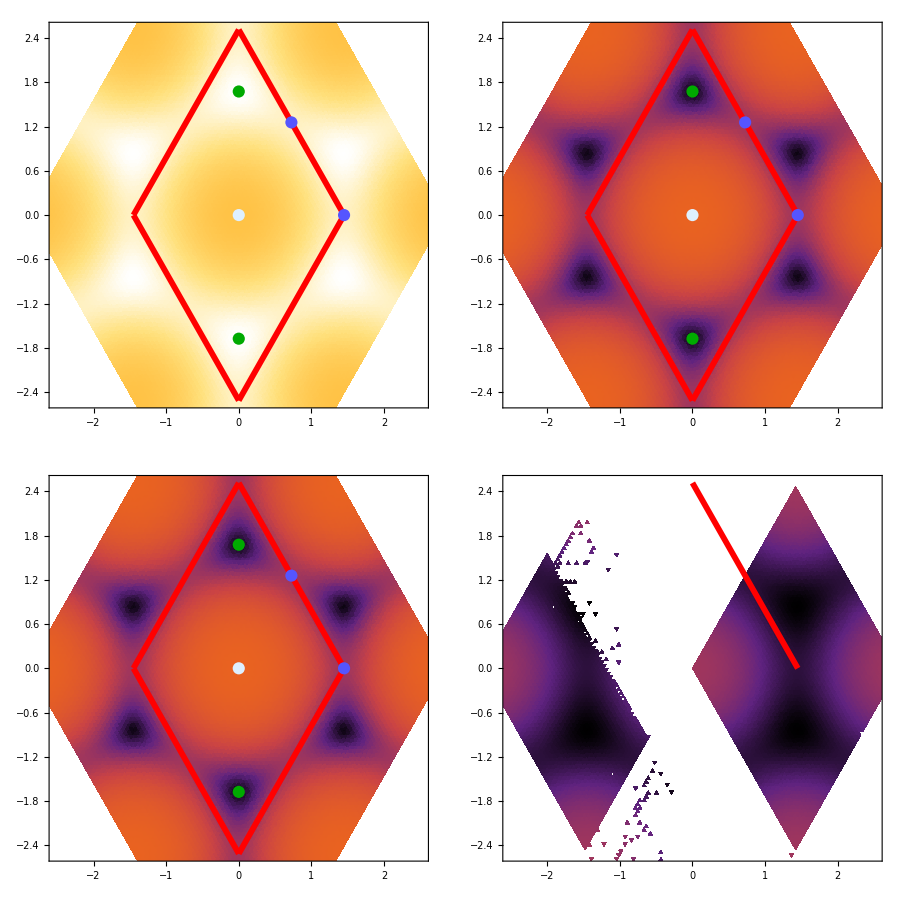

```mathematica
GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiled[[11]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->False,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]]
```

### export to pdf

```mathematica
Do[
Block[{plts},
plts=GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiled[[step+1]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->False,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]];
Export["./DensityMatrix_k_it"<>ToString[step*plotsteps]<>".pdf",Style[plts,Background->White],"AllowRasterization"->True,ImageResolution->800];
],{step,0,printsteps/plotsteps}]
```

## DensityMatrix_k_bloch

### DensityMatrix_k_bloch in time steps

```mathematica
densmatbloch=ParallelTable[Flatten[Table[Import[tt,"DensityMatrix_k_bloch/"<>ToString[step]<>"/"<>ToString[i-1]<>"/local"],{i,1,ncom}]],{step,0,printsteps,plotsteps}];
reimdensmatbloch=ParallelTable[Partition[densmatbloch[[step+1]],2]/.{x_,y_}->{x+ⅈ y},{step,0,printsteps/plotsteps}];
reshapeddensmatbloch=ParallelTable[ArrayReshape[reimdensmatbloch[[step+1]],{numkpts,numbands,numbands}],{step,0,printsteps/plotsteps}];
```

```mathematica
(Dimensions[densmatbloch][[2]])/(numkpts*numbands^2*2)
```

1

```mathematica
Length[reshapeddensmatbloch]
```

11

### tiled DensityMatrix_k_bloch

```mathematica
tiledbloch=ParallelTable[Module[{popkptscond},

popkptscond[a_,b_]:=Table[{kptstrans[[i,1]],
kptstrans[[i,2]],Abs[reshapeddensmatbloch[[step+1]][[i,a,b]]]},{i,1,Length[kpts]}];
Table[Flatten[Table[popkptscond[a,b]+Threaded[shift[[i]]],{i,1,Length[shift]}],1],{a,1,numbands},{b,1,numbands}]
],{step,0,printsteps/plotsteps}];
```

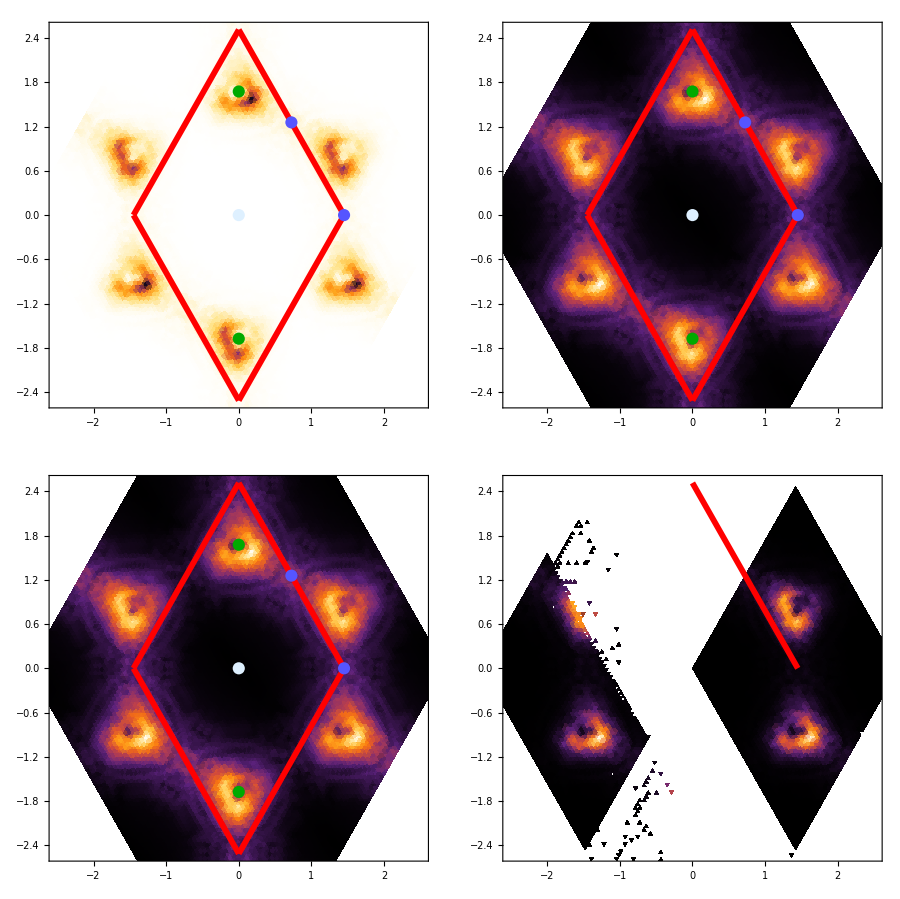

```mathematica
GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiledbloch[[(step+1)/.step->5]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->True,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]]
```

### export to pdf

```mathematica
Do[
Block[{plts},
plts=GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiledbloch[[step+1]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->True,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]];
Export["./DensityMatrix_k_bloch_it"<>ToString[step*plotsteps]<>".pdf",Style[plts,Background->White],"AllowRasterization"->True,ImageResolution->800];
],{step,0,printsteps/plotsteps}]
```

## fullH

### fullH in time steps

```mathematica
hammat=ParallelTable[Flatten[Table[Import[tt,"fullH/"<>ToString[step]<>"/"<>ToString[i-1]<>"/local"],{i,1,ncom}]],{step,0,printsteps,plotsteps}];
reimhammat=ParallelTable[Partition[hammat[[step+1]],2]/.{x_,y_}->{x+ⅈ y},{step,0,printsteps/plotsteps}];
reshapedHamMat=ParallelTable[ArrayReshape[reimhammat[[step+1]],{numkpts,numbands,numbands}],{step,0,printsteps/plotsteps}];
```

```mathematica
(Dimensions[hammat][[2]])/(numkpts*numbands^2*2)
```

1

```mathematica
Length[reshapedHamMat]
```

11

### tiled fullH

```mathematica
tiledHam=ParallelTable[Module[{popkptscond},

popkptscond[a_,b_]:=Table[{kptstrans[[i,1]],
kptstrans[[i,2]],Abs[reshapedHamMat[[step+1]][[i,a,b]]]},{i,1,Length[kpts]}];
Table[Flatten[Table[popkptscond[a,b]+Threaded[shift[[i]]],{i,1,Length[shift]}],1],{a,1,numbands},{b,1,numbands}]
],{step,0,printsteps/plotsteps}];
```

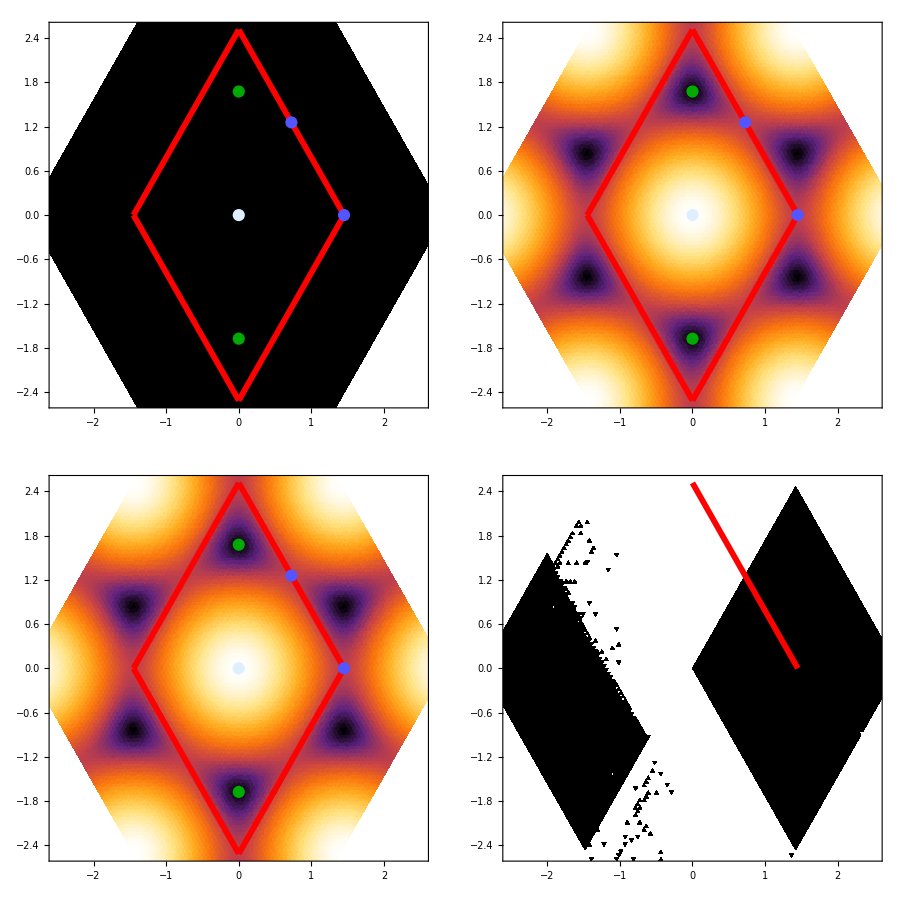

```mathematica
GraphicsGrid[
ParallelTable[
Show[{
ListDensityPlot[
{
tiledHam[[1]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]]
```

### export to pdf

```mathematica
Do[
Block[{plts},
plts=GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiledHam[[step+1]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->True,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]];
Export["./fullH_it"<>ToString[step*plotsteps]<>".pdf",Style[plts,Background->White],"AllowRasterization"->True,ImageResolution->800];
],{step,0,printsteps/plotsteps}]
```

## SelfEnergy

### SelfEnergy in time steps

```mathematica
selfener=ParallelTable[Flatten[Table[Import[tt,"SelfEnergy/"<>ToString[step]<>"/"<>ToString[i-1]<>"/local"],{i,1,ncom}]],{step,0,printsteps,plotsteps}];
reimselfener=ParallelTable[Partition[selfener[[step+1]],2]/.{x_,y_}->{x+ⅈ y},{step,0,printsteps/plotsteps}];
reshapedselfener=ParallelTable[ArrayReshape[reimselfener[[step+1]],{numkpts,numbands,numbands}],{step,0,printsteps/plotsteps}];
```

```mathematica
(Dimensions[selfener][[2]])/(numkpts*numbands^2*2)
```

1

```mathematica
Length[reshapedselfener]
```

11

### tiled SelfEnergy

```mathematica
tiledSE=ParallelTable[Module[{popkptscond},

popkptscond[a_,b_]:=Table[{kptstrans[[i,1]],
kptstrans[[i,2]],Abs[reshapedselfener[[step+1]][[i,a,b]]]},{i,1,Length[kpts]}];
Table[Flatten[Table[popkptscond[a,b]+Threaded[shift[[i]]],{i,1,Length[shift]}],1],{a,1,numbands},{b,1,numbands}]
],{step,0,printsteps/plotsteps}];
```

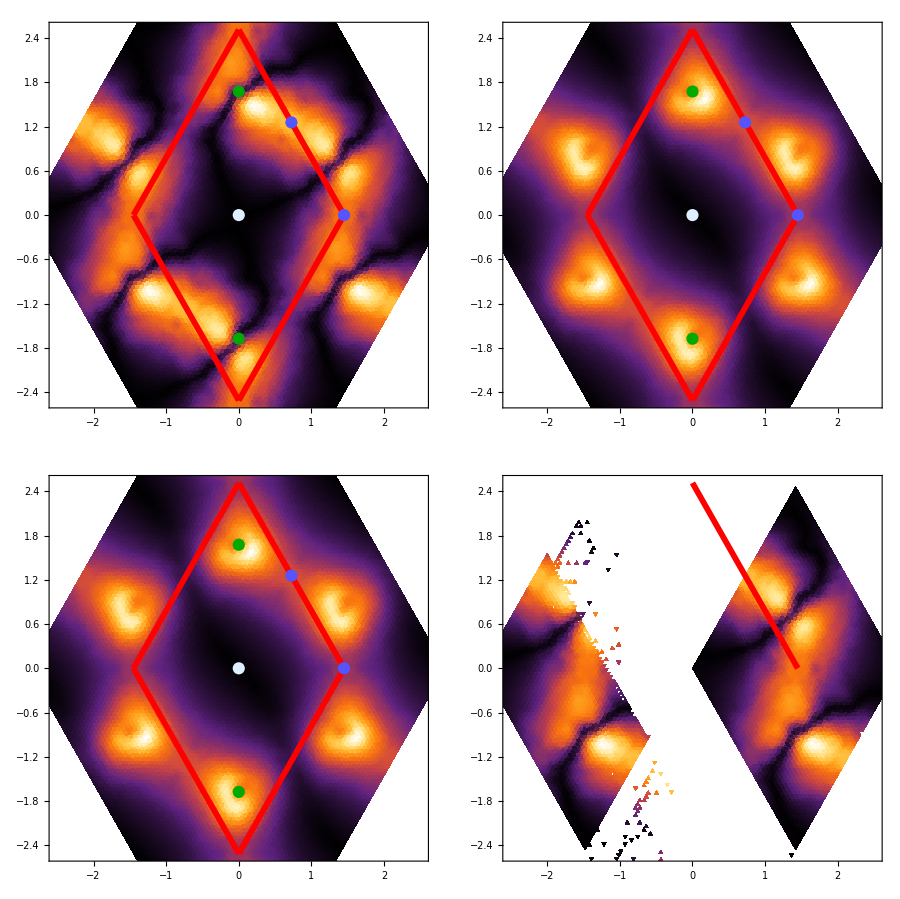

```mathematica
GraphicsGrid[
ParallelTable[
Show[{
ListDensityPlot[
{
tiledSE[[6]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]]
```

### export to pdf

```mathematica
Do[
Block[{plts},
plts=GraphicsGrid[ParallelTable[
Show[{
ListDensityPlot[
{
tiledSE[[step+1]][[i,j]]
}
,ImageSize->350,ColorFunction->"SunsetColors",ColorFunctionScaling->True,Ticks->{Automatic,Automatic,None},PlotRange->{{-corner3[[2]],corner3[[2]]},{-corner3[[2]],corner3[[2]]},Full}] ,
lattice
}]
,{i,1,2},{j,1,2}],ImageSize->900,Spacings->Scaled[0.025]];
Export["./SelfEnergy_it"<>ToString[step*plotsteps]<>".pdf",Style[plts,Background->White],"AllowRasterization"->True,ImageResolution->800];
],{step,0,printsteps/plotsteps}]
```